```mathematica
(*clear any existing parameters*)
Clear[β,δ,λ,ρ,d,s,r]
```

```mathematica
(*setup the original metapopulation model equations*)
```

```mathematica
f0a=λ((1-δ)* (Exp[x1a]+Exp[x2a]+Exp[x3a])+δ* ( Exp[x1b]+ Exp[x2b]+Exp[x3b]));
f1a= Exp[ζa] Exp[x0a] Exp[−β Log[Exp[x0a]]];
f2a=(1-δ)* λ Exp[x1a]+δ* λ Exp[x1b];
f3a=(1-δ)* λ Exp[x2a]+δ* λ Exp[x2b]+(1-δ)* λ Exp[x3a]+δ* λ Exp[x3b];
f0b=λ((1-δ) *(Exp[x1b]+Exp[x2b]+Exp[x3b])+δ* ( Exp[x1a]+ Exp[x2a]+Exp[x3a]));
f1b=   Exp[ζb]*Exp[x0b]* Exp[−β  Log[ Exp[x0b]]];
f2b=(1-δ)*λ Exp[x1b]+δ*λ Exp[x1a];
f3b=(1-δ)* λ Exp[x2b]+δ*λ Exp[x2a]+(1-δ)* λ Exp[x3b]+δ*λ Exp[x3a];
```

```mathematica
(*differentiate the log-scale model to yield the Jacobian *)
```

```mathematica
F1[f1_,f2_]:=D[Log[f1],f2]
J:=Outer[F1,{f0a,f1a,f2a,f3a,f0b,f1b,f2b,f3b},{x0a,x1a,x2a,x3a,x0b,x1b,x2b,x3b}]

(*Evaluate the Jacobian at the equilibrium*)
Jeq=Simplify[J/.x3a->x2a+Log[λ]/.x2a->x1a+Log[λ]/. x3b->x2b+Log[λ]/.x2b->x1b+Log[λ]/. x1a->x1/.x1b->x1/.x0b->x0/.x0a->x0];
MatrixForm[Jeq]
```

(0 | (1-δ)/(1+λ+λ^2) | (λ-δ λ)/(1+λ+λ^2) | -((-1+δ) λ^2)/(1+λ+λ^2) | 0 | δ/(1+λ+λ^2) | (δ λ)/(1+λ+λ^2) | (δ λ^2)/(1+λ+λ^2)
1-β | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1-δ | 0 | 0 | 0 | δ | 0 | 0
0 | 0 | (1-δ)/(1+λ) | (λ-δ λ)/(1+λ) | 0 | 0 | δ/(1+λ) | (δ λ)/(1+λ)
0 | δ/(1+λ+λ^2) | (δ λ)/(1+λ+λ^2) | (δ λ^2)/(1+λ+λ^2) | 0 | (1-δ)/(1+λ+λ^2) | (λ-δ λ)/(1+λ+λ^2) | -((-1+δ) λ^2)/(1+λ+λ^2)
0 | 0 | 0 | 0 | 1-β | 0 | 0 | 0
0 | δ | 0 | 0 | 0 | 1-δ | 0 | 0
0 | 0 | δ/(1+λ) | (δ λ)/(1+λ) | 0 | 0 | (1-δ)/(1+λ) | (λ-δ λ)/(1+λ))

```mathematica
(*Generate the A matrix of stochastic inputs*)
A:=Outer[F1,{f0a,f1a,f2a,f3a,f0b,f1b,f2b,f3b},{ζa,ζb}];
MatrixForm[A]
```

(0 | 0
1 | 0
0 | 0
0 | 0
0 | 0
0 | 1
0 | 0
0 | 0)

```mathematica
(*Function to generate a covariance matrix from variance and correlation values*)
CovMat[sigma_ ,rho_]:=DiagonalMatrix[{sigma,sigma}].(Reverse[DiagonalMatrix[Table[rho,2]]]+DiagonalMatrix[Table[1,2]]).DiagonalMatrix[{sigma,sigma}]
```

```mathematica
(*Get input values from the Jacobian to generate a function*)
InputForm[Jeq]
```

{{0, (1 - δ)/(1 + λ + λ^2), (λ - δ*λ)/(1 + λ + λ^2), -(((-1 + δ)*λ^2)/(1 + λ + λ^2)), 
  0, δ/(1 + λ + λ^2), (δ*λ)/(1 + λ + λ^2), (δ*λ^2)/(1 + λ + λ^2)}, 
 {1 - β, 0, 0, 0, 0, 0, 0, 0}, {0, 1 - δ, 0, 0, 0, δ, 0, 0}, 
 {0, 0, (1 - δ)/(1 + λ), (λ - δ*λ)/(1 + λ), 0, 0, δ/(1 + λ), (δ*λ)/(1 + λ)}, 
 {0, δ/(1 + λ + λ^2), (δ*λ)/(1 + λ + λ^2), (δ*λ^2)/(1 + λ + λ^2), 0, 
  (1 - δ)/(1 + λ + λ^2), (λ - δ*λ)/(1 + λ + λ^2), -(((-1 + δ)*λ^2)/(1 + λ + λ^2))}, 
 {0, 0, 0, 0, 1 - β, 0, 0, 0}, {0, δ, 0, 0, 0, 1 - δ, 0, 0}, 
 {0, 0, δ/(1 + λ), (δ*λ)/(1 + λ), 0, 0, (1 - δ)/(1 + λ), (λ - δ*λ)/(1 + λ)}}

```mathematica
(*Set the above as the jacobian (need to copy and paste the function)*)
```

```mathematica
jac[β_,δ_,λ_]:=
{{0,(1-δ)/(1+λ+λ^2),(λ-δ*λ)/(1+λ+λ^2),-(((-1+δ)*λ^2)/(1+λ+λ^2)),0,δ/(1+λ+λ^2),(δ*λ)/(1+λ+λ^2),(δ*λ^2)/(1+λ+λ^2)},{1-β,0,0,0,0,0,0,0},{0,1-δ,0,0,0,δ,0,0},{0,0,(1-δ)/(1+λ),(λ-δ*λ)/(1+λ),0,0,δ/(1+λ),(δ*λ)/(1+λ)},{0,δ/(1+λ+λ^2),(δ*λ)/(1+λ+λ^2),(δ*λ^2)/(1+λ+λ^2),0,(1-δ)/(1+λ+λ^2),(λ-δ*λ)/(1+λ+λ^2),-(((-1+δ)*λ^2)/(1+λ+λ^2))},{0,0,0,0,1-β,0,0,0},{0,δ,0,0,0,1-δ,0,0},{0,0,δ/(1+λ),(δ*λ)/(1+λ),0,0,(1-δ)/(1+λ),(λ-δ*λ)/(1+λ)}}
```

```mathematica
(*Function to calculate volatility vector*)
SSV[β_,δ_,λ_,s_,r_]:=Sqrt[Exp[Diagonal[(jac[β,δ,λ]).(A.CovMat[s,r].Transpose[A]).Transpose[(jac[β,δ,λ])]+
(MatrixPower[jac[β,δ,λ],2]).(A.CovMat[s,r].Transpose[A]).Transpose[MatrixPower[jac[β,δ,λ],2]]]]-1]

FullSimplify[SSV[b,δ,λ,1,-0.45]][[1,1]]
```

-1+ⅇ^((1.+δ (-2.9+2.9 δ)+(1.+δ (-5.8+δ (17.4+δ (-23.2+11.6 δ)))) λ^2)/((1.+λ+λ^2)^2))

```mathematica
(*Function to calculate Long-Run Covariance Matrix*)
Sigma1[β_,δ_,λ_,s_,r_]:=
Partition[(Inverse[IdentityMatrix[Dimensions[Jeq][[1]]^2]-KroneckerProduct[jac[β,δ,λ],jac[β,δ,λ]]]). (Flatten[A.CovMat[s,r].Transpose[A]]),Dimensions[Jeq][[1]]]
```

```mathematica
(*Functions to calculate Spatial Variabibility, coefficient of variation, spatial correlations, and autocorrelations*)
SpatVar[β_,δ_,λ_,s_,r_]:=(0.5*(Exp[Sigma1[β,δ,λ,s,r][[1,1]]]-1)-0.5*(Exp[Sigma1[β,δ,λ,s,r][[1,5]]]-1))
PopCV[β_,δ_,λ_,s_,r_]:=(Exp[Sigma1[β,δ,λ,s,r][[1,1]]]-1)
MetapopCV[β_,δ_,λ_,s_,r_]:=0.5*((Exp[Sigma1[β,δ,λ,s,r][[1,1]]]-1)+(Exp[Sigma1[β,δ,λ,s,r][[1,5]]]-1))
ImpulseResponse[β_,δ_,λ_,n_]:=MatrixPower[jac[β,δ,λ],n].(A[[All,1]])
AutoCorr[β_,δ_,λ_,s_,r_]:=Sqrt[Inverse[DiagonalMatrix[Diagonal[Sigma1[β,δ,λ,s,r]]]]].((jac[β,δ,λ].Sigma1[β,δ,λ,s,r])).Sqrt[Inverse[DiagonalMatrix[Diagonal[Sigma1[β,δ,λ,s,r]]]]]
SpatCor[β_,δ_,λ_,s_,r_]:=(Sqrt[Inverse[DiagonalMatrix[Diagonal[Sigma1[β,δ,λ,s,r]]]]].((Sigma1[β,δ,λ,s,r])).Sqrt[Inverse[DiagonalMatrix[Diagonal[Sigma1[β,δ,λ,s,r]]]]])[[1,5]]
FirstAutoCorr[β_,δ_,λ_,s_,r_]:=AutoCorr[β,δ,λ,s,r][[1,1]]
```

```mathematica
A
```

{{0,0},{1,0},{0,0},{0,0},{0,0},{0,1},{0,0},{0,0}}

```mathematica
(*Generate the First Order Impulse Responses*)

MatrixPower[jac[β,δ,λ],1].(A[[All,1]])
```

{(1-δ)/(1+λ+λ^2),0,1-δ,0,δ/(1+λ+λ^2),0,δ,0}

```mathematica
(*Generate the figures*)

beta= 0.99;varmax=0.3;sigma =1;IS=240;delta1=0.25;delta2=0.15;d1=0;
```

```mathematica
FS = 12;
cm=72/2.54;
```

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->FS,FontFamily->"Arial",FractionBoxOptions->{Beveled->True}},AxesStyle->{FontSize->FS,FontFamily->"Arial"},LabelStyle->{FontSize->FS,FontFamily->"Arial",Black},TicksStyle->{{FontSize->FS,FontFamily->"Arial",Black},{FontSize->FS,FontFamily->"Arial",Black}},Frame->True,
AspectRatio->0.75,GridLines->None];
```

```mathematica
F1a:=Plot[{FirstAutoCorr[beta,delta1,Exp[-x],sigma,-0.45],
SpatCor[beta,delta1,Exp[-x],sigma,-0.45] ,
ImpulseResponse[beta,delta1,Exp[-x],1][[1]] },
{x,0.2,2},
PlotRange->{{0.2,2},{0,0.7}},
PlotStyle->{{Black,Thickness[0.016]},
{Directive[Dotted],Black,Thickness[0.005]},
{Directive[RGBColor[240/255,59/255,32/255]],Thickness[0.006]}},
BaseStyle->{FontSize->FS,FontFamily->"Arial"},
AxesStyle->{FontFamily->"Sans",FontSize->FS},
LabelStyle->{FontSize->FS,FontFamily->"Arial",Black},
AxesOrigin ->{0.25,0},
AspectRatio->1,
ImageSize->8.7cm,
Frame->True,
FrameLabel->{{Column[{Row[{Style["Temporal (",FontSize->FS,FontFamily->"Arial"],Graphics[{Thickness[0.25],Line[{{0.01,0},{0,0}}]},AspectRatio->0.2,ImageSize->15],Style[") or Spatial (",FontFamily->"Arial",FontSize->FS],Graphics[{Dotted,Thickness[0.12],Line[{{0.01,0},{0,0}}]},AspectRatio->0.2,ImageSize->15],Style[")",FontSize->FS,FontFamily->"Arial"]}],Style["Autocorrelation",FontFamily->"Arial",FontSize->FS]},Alignment->Center],Rotate[Style["Envir. Impulse Response (*)",FontSize->FS,FontFamily->"Arial",Directive[RGBColor[240/255,59/255,32/255]]],180Degree]},{"Mortality (Natural+Harvest)",None}},
FrameTicks->{{{0,0.2,0.4,0.6},None},{{0.05,0.4,0.8,1.2,1.6,2},None}},
Axes->False,Frame->False,
Epilog->{{Text[Style["(c)",TextAlignment->Center,FontSize->14,Bold],Scaled[{.1,.1}]]},{Text[Rotate[Style[Superscript["Sensitivity","*"],TextAlignment->Center,FontSize->12,Directive[RGBColor[240/255,59/255,32/255]]],25Degree],Scaled[{.6,.83}]]},
{Text[Rotate[Style["Predictability",TextAlignment->Center,FontSize->12],-44Degree],Scaled[{.18,.75}]]},
{Text[Rotate[Style["Coupling",TextAlignment->Center,FontSize->12,Black],-21Degree],Scaled[{.21,.39}]]}}];
```

```mathematica
F1b:=Plot[FirstAutoCorr[beta,delta1,Exp[-x]-0.04,sigma,-0.45]+0.08,{x,.78,1},
PlotStyle->{Black,Thickness[0.005]},
PlotRange->{{0.2,2},{0,0.7}},
PlotStyle->{{Black,Thickness[0.016]},
{Directive[Dotted],Black,Thickness[0.005]},
{Directive[RGBColor[240/255,59/255,32/255]],Thickness[0.006]}},
BaseStyle->{FontSize->FS,FontFamily->"Arial"},
AxesStyle->{FontFamily->"Sans",FontSize->FS},
LabelStyle->{FontSize->FS,FontFamily->"Arial",Black},
AxesOrigin ->{0.25,0},
AspectRatio->1,
ImageSize->8.7cm,
Frame->True,
FrameLabel->{{Column[{Row[{Style["Temporal (",FontSize->FS,FontFamily->"Arial"],Graphics[{Thickness[0.25],Line[{{0.01,0},{0,0}}]},AspectRatio->0.2,ImageSize->15],Style[") or Spatial (",FontFamily->"Arial",FontSize->FS],Graphics[{Dotted,Thickness[0.12],Line[{{0.01,0},{0,0}}]},AspectRatio->0.2,ImageSize->15],Style[")",FontSize->FS,FontFamily->"Arial"]}],Style["Autocorrelation",FontFamily->"Arial",FontSize->FS]},Alignment->Center],Rotate[Style["Envir. Impulse Response (*)",FontSize->FS,FontFamily->"Arial",Directive[RGBColor[240/255,59/255,32/255]]],180Degree]},{"Mortality (Natural+Harvest)",None}},
FrameTicks->{{{0,0.2,0.4,0.6},None},{{0.05,0.4,0.8,1.2,1.6,2},None}},
Axes->False,Frame->False,
Epilog->{{Text[Style["(c)",TextAlignment->Center,FontSize->14,Bold],Scaled[{.1,.1}]]},{Text[Rotate[Style[Superscript["Sensitivity","*"],TextAlignment->Center,FontSize->12,Directive[RGBColor[240/255,59/255,32/255]]],25Degree],Scaled[{.6,.83}]]},
{Text[Rotate[Style["Predictability",TextAlignment->Center,FontSize->12],-44Degree],Scaled[{.18,.75}]]},
{Text[Rotate[Style["Coupling",TextAlignment->Center,FontSize->12,Black],-21Degree],Scaled[{.21,.39}]]}}];
```

```mathematica
F1c:=Plot[SpatCor[beta,delta1,Exp[-x]-0.05,sigma,-0.45]-0.02,{x,.85,1.15},
PlotRange->{{0.2,2},{0,0.7}},
PlotStyle->{{Black,Thickness[0.005]},
{Directive[Dotted],Black,Thickness[0.005]},
{Directive[RGBColor[240/255,59/255,32/255]],Thickness[0.006]}},
BaseStyle->{FontSize->FS,FontFamily->"Arial"},
AxesStyle->{FontFamily->"Sans",FontSize->FS},
LabelStyle->{FontSize->FS,FontFamily->"Arial",Black},
AxesOrigin ->{0.25,0},
AspectRatio->1,
ImageSize->8.7cm,
Frame->True,
FrameLabel->{{Column[{Row[{Style["Temporal (",FontSize->FS,FontFamily->"Arial"],Graphics[{Thickness[0.25],Line[{{0.01,0},{0,0}}]},AspectRatio->0.2,ImageSize->15],Style[") or Spatial (",FontFamily->"Arial",FontSize->FS],Graphics[{Dotted,Thickness[0.12],Line[{{0.01,0},{0,0}}]},AspectRatio->0.2,ImageSize->15],Style[")",FontSize->FS,FontFamily->"Arial"]}],Style["Autocorrelation",FontFamily->"Arial",FontSize->FS]},Alignment->Center],Rotate[Style["Envir. Impulse Response (*)",FontSize->FS,FontFamily->"Arial",Directive[RGBColor[240/255,59/255,32/255]]],180Degree]},{"Mortality (Natural+Harvest)",None}},
FrameTicks->{{{0,0.2,0.4,0.6},None},{{0.05,0.4,0.8,1.2,1.6,2},None}},
Axes->False,Frame->False,
Epilog->{{Text[Style["(c)",TextAlignment->Center,FontSize->14,Bold],Scaled[{.1,.1}]]},{Text[Rotate[Style[Superscript["Sensitivity","*"],TextAlignment->Center,FontSize->12,Directive[RGBColor[240/255,59/255,32/255]]],25Degree],Scaled[{.6,.83}]]},
{Text[Rotate[Style["Predictability",TextAlignment->Center,FontSize->12],-44Degree],Scaled[{.18,.75}]]},
{Text[Rotate[Style["Coupling",TextAlignment->Center,FontSize->12,Black],-21Degree],Scaled[{.21,.39}]]}}];
```

```mathematica
F1d:=Plot[ImpulseResponse[beta,delta1,Exp[-x],1][[1]]+0.03  ,
{x,1.6,1.9},
PlotStyle->{Directive[RGBColor[215/255,48/255,31/255]],Thickness[0.005]},
PlotRange->{{0.2,2},{0,0.7}},
PlotStyle->{{Black,Thickness[0.016]},
{Directive[Dotted],Black,Thickness[0.005]},
{Directive[RGBColor[240/255,59/255,32/255]],Thickness[0.006]}},
BaseStyle->{FontSize->FS,FontFamily->"Arial"},
AxesStyle->{FontFamily->"Sans",FontSize->FS},
LabelStyle->{FontSize->FS,FontFamily->"Arial",Black},
AxesOrigin ->{0.25,0},
AspectRatio->1,
ImageSize->8.7cm,
Frame->True,
FrameLabel->{{Column[{Row[{Style["Temporal (",FontSize->FS,FontFamily->"Arial"],Graphics[{Thickness[0.25],Line[{{0.01,0},{0,0}}]},AspectRatio->0.2,ImageSize->15],Style[") or Spatial (",FontFamily->"Arial",FontSize->FS],Graphics[{Dotted,Thickness[0.12],Line[{{0.01,0},{0,0}}]},AspectRatio->0.2,ImageSize->15],Style[")",FontSize->FS,FontFamily->"Arial"]}],Style["Autocorrelation",FontFamily->"Arial",FontSize->FS]},Alignment->Center],Rotate[Style["Envir. Impulse Response (*)",FontSize->FS,FontFamily->"Arial",Directive[RGBColor[240/255,59/255,32/255]]],180Degree]},{"Mortality (Natural+Harvest)",None}},
FrameTicks->{{{0,0.2,0.4,0.6},None},{{0.05,0.4,0.8,1.2,1.6,2},None}},
Axes->False,Frame->False,
Epilog->{{Text[Style["(c)",TextAlignment->Center,FontSize->14,Bold],Scaled[{.1,.1}]]},{Text[Rotate[Style[Superscript["Sensitivity","*"],TextAlignment->Center,FontSize->12,Directive[RGBColor[240/255,59/255,32/255]]],25Degree],Scaled[{.6,.83}]]},
{Text[Rotate[Style["Predictability",TextAlignment->Center,FontSize->12],-44Degree],Scaled[{.18,.75}]]},
{Text[Rotate[Style["Coupling",TextAlignment->Center,FontSize->12,Black],-21Degree],Scaled[{.21,.39}]]}}];
```

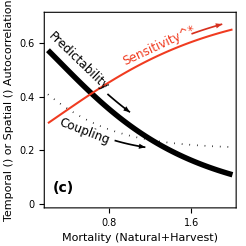

```mathematica
Figure1c:=Show[{F1b/.Line->Arrow,F1c/.Line->Arrow,F1d/.Line->Arrow,F1a}]
Figure1c
```

```mathematica
CorAd[β_,δ_,λ_,s_,r_]:=Sigma1[β,δ,λ,s,r][[1,5]]/(Sqrt[Sigma1[β,δ,λ,s,r][[1,1]]]*Sqrt[Sigma1[β,δ,λ,s,r][[6,6]]])
```

```mathematica
Row@{Style[Superscript["Temporal",†]],Spacer[1],Style[Superscript["Spatial",†]]}
```

Temporal^†Spatial^†

```mathematica
VP:={4,-5,2}
d1=0;
SetOptions[Plot3D,BaseStyle->{FontFamily->"Arial",FontSize->FS},LabelStyle->{FontFamily->"Arial",FontSize->FS,Black}];
VP:={4.5,5,2}
d1=0;
beta= 0.99;
lambda=0.45;
lambda2=0.9;
cvmax= 0.75;
sigma =1;IS=8.7cm;delta1=0.25;delta2=0.15;
```

```mathematica
VP:={4,-5,2}
d1=0;
beta= 0.9;lambda=0.45;lambda2=0.9;cvmax= 0.66;sigma =1;IS=300;delta1=0.25;delta2=0.15;
F2a:=Plot3D[PopCV[beta,x,lambda,sigma,(2*y-1)],{x,0.05,.35},{y,0.05,0.9},
PlotRange->{{0.05,.35},{0.05,.9},{0,.6}},
PlotStyle->Opacity[0.6],
Ticks->{{0.1,0.2,0.3},{0.2,0.5,0.8},{0,0.3,0.6}},
ColorFunction->ColorData[{"DeepSeaColors",{0,cvmax}}],ColorFunctionScaling->False,
ImageSize->8.5cm,BoxRatios->{1,1,0.8},ViewPoint->VP,
Epilog->{Text[Style["(b)",TextAlignment->Center,FontSize->16,Bold],Scaled[{.95,1}]]}]
F2b:=Plot3D[MetapopCV[beta,x,lambda,sigma,(2*y-1)],{x,0.05,.35},{y,0.05,0.9},
PlotRange->{{0.05,.35},{0.05,.9},{0,cvmax}},
ImageSize->8.5cm,
PlotStyle->Opacity[0.4],ColorFunction->ColorData[{"GrayTones",{-1,1}}],BoxRatios->{1,1,0.8},ViewPoint->VP]
Show[F2a,F2b]
```

-Graphics3D-

```mathematica
SetOptions[Plot3D,BaseStyle->{FontFamPly->"Arial",FontSize->12},LabelStyle->{FontFamily->"Arial",FontSize->12,Black}];
VP:={4,-5,2}
d1=0;
beta= 0.9;lambda=0.45;lambda2=0.9;varmax=0.3;sigma =1;IS=240;delta1=0.25;delta2=0.15;d1=0;
Figure1a:=Plot[{SpatVar[beta,0.25,Exp[-x],sigma,-0.6],
SpatVar[beta,0.25,Exp[-x],sigma,0],
SpatVar[beta,0.25,Exp[-x],sigma,0.6]}
 ,{x,0.2,2},
PlotTheme->"Monochrome",
PlotRange->{{0.2,2},{0,.2}},
PlotStyle->{{Black,Thickness[0.008]}},
BaseStyle->{FontSize->FS},
GridLinesStyle->Directive[Thin,Black],
LabelStyle->{FontSize->FS,Black},
AxesOrigin ->{0.25,0},
ImageSize->8.5cm,
Frame->True,
AspectRatio->0.97,
FrameTicks->{{{0,0.1,0.2},None},{{0.4,0.8,1.2,1.6,2},None}},
Axes->True,
FrameLabel ->{Style["Mortality (Natural+Harvest)",FontFamily->"Arial",FontSize->FS],"Spatial Variation"},
PlotLegends->{Placed[LineLegend[{0.2,0.5,0.8},
LegendLabel->Placed["Recruitment\nSynchrony",Row],LegendLayout->"Column",
LegendMarkerSize->{25,1.2},Spacings->{0.1,0.25},LabelStyle->{FontSize->FS,TextAlignment->Top}],{0.18,0.7}]},
Epilog->{Text[Style["(a)",TextAlignment->Center,FontSize->14,Bold],Scaled[{.8,.9}]]}];
PlotLegend1:=Plot[Im[(-1)^x],{x,0,2},
PlotRange->{{0.1,.5},{-0.9,.9}},
PlotStyle->Opacity[0],Axes->False,Frame->False,
ImageSize->8.2cm,
PlotLegends->{Placed[SwatchLegend[{ColorData[{"DeepSeaColors",{0,cvmax}},0.6],LightGray},{"Pop.","Metapop"},
LegendMarkerSize->Large,
LegendMarkers->Automatic,
LabelStyle->{FontSize->FS,FontFamily->"Arial"},
LegendLayout->{"Column",1}],{0.85,0.1}]}];
Figure :=Grid[{{Show[Figure1a,ImageSize->8.5cm],Overlay[{Rasterize[Show[F2a,F2b,
Graphics3D[Text[Rotate[Style["Migration (δ)",FontSize->FS,FontFamily->"Arial"],-14Degree],{0.1,0.5,-.4}]],
Graphics3D[Text[Rotate[Style["Recruitment Synchrony",FontSize->FS,FontFamily->"Arial"],14.5 Degree],{0.05,0.38,0.73}]],
Graphics3D[Text[Rotate[Style["Temporal Variation (CV^2)",FontSize->FS,FontFamily->"Arial"],90 Degree],{0.05,-0.25,0.45}]],ImageSize->8.7cm],ImageResolution->1200,Background->None],PlotLegend1}],Show[Figure1c,ImageSize->9.5cm]}}];
```

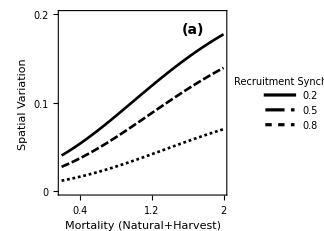
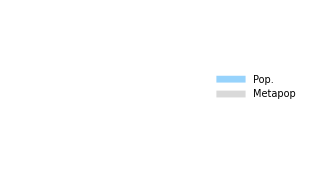
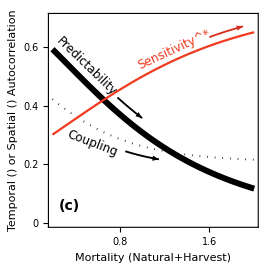
-Graphics- | -Graphics--Graphics- | -Graphics-

```mathematica
Figure
```